# Modelo versión 3

## Pruebas 30/07

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ivals={100,200,300,400,500,600,700,800,900,1000};
jvals={1000,2000,3000,4000,5000,6000,7000,8000,9000,10000};
networksM3=Table[Import[StringJoin["graphs/model-v3/capacity1/","network-",IntegerString[ivals[[i]]],"-",IntegerString[jvals[[i]]],".graphml"]],{i,1,10,1}];
```

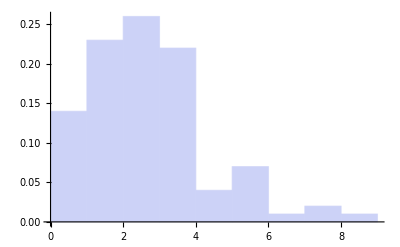
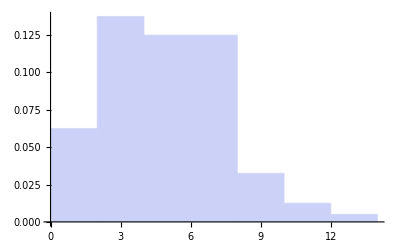
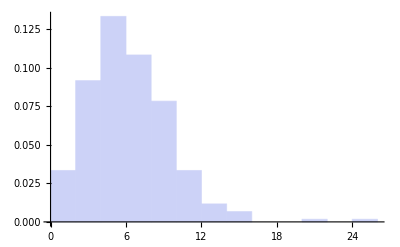
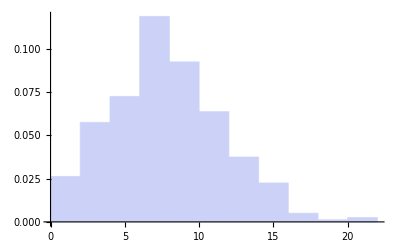
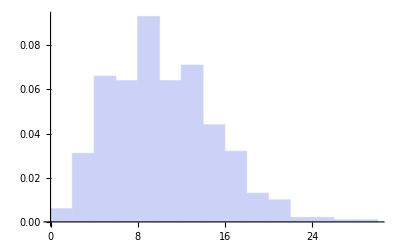
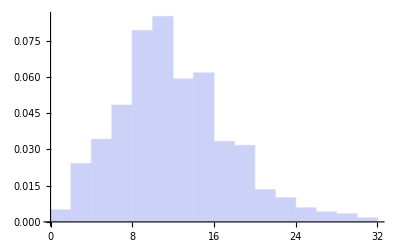
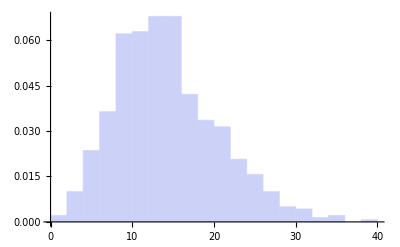
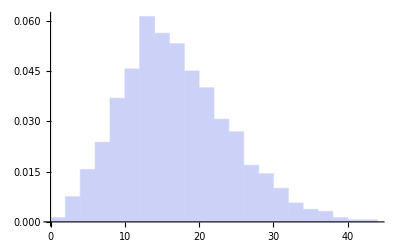

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,10,1}]
```

{57/271,111/718,450/2881,1686/12109,3945/27233,59/408,5484/37715,1308/8695,3936/26309,15585/106003}

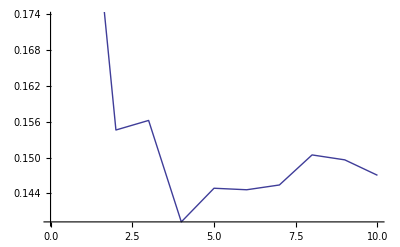

{∞,∞,∞,∞,∞,∞,∞,880321/319600,∞,675241/249750}

-Graphics-

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3]
ListPlot[clusteringM3,Joined->True]
aplM3=Map[MeanGraphDistance,networksM3]
ListPlot[aplM3,Joined->True]
```